```mathematica
ReVc[r_,mD_,α_]:=-mD α-(ⅇ^(-mD r) α)/r;
```

```mathematica
ReEc[r_,mD_,α_]:=α ExpIntegralEi[-mD r];
```

```mathematica
ImVc[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
```

```mathematica
ImEc[r_,mD_,α_,T_]:=T α 1/4 √π r MeijerG[{{0,1/2},{}},{{0,1},{-1/2,-1/2}},(mD^2 r^2)/4];
```

```mathematica
ReVs[r_,mD_,σ_]:=(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
```

```mathematica
ReEs[r_,mD_,σ_]:=(ⅇ^(-mD r) (-3/mD-r) σ)/mD;
```

```mathematica
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImEs[r_,mD_,σ_,T_]:=1/8 mD √π r^4 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-2,-3/2}},(mD^2 r^2)/4];
```

```mathematica
Vc0[r_,α_]:=-α/r;
```

```mathematica
Ec0[r_,α_]:=α/r^2;
```

```mathematica
Vs0[r_,σ_]:=σ r;
```

```mathematica
Es0[r_,σ_]:=-σ;
```

```mathematica
Integrate[Ec0[r,α] r^2 ReEc[r,mD,α],r]
```

α^2 (ⅇ^(-mD r)/mD+r ExpIntegralEi[-mD r])

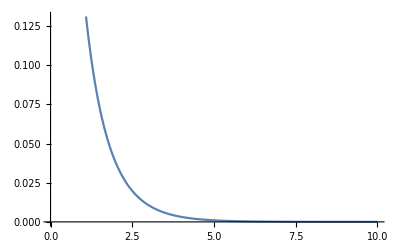

```mathematica
Block[{α=1,mD=1},Plot[α^2 (ⅇ^(-mD r)/mD+r ExpIntegralEi[-mD r]),{r,0,10}]]
```

```mathematica
Integrate[Ec0[r,α] r^2 ImEc[r,mD,α,T],r]
```

(√π T α^2 MeijerG[{{1,1,3/2},{}},{{1,2},{0,1/2,1/2}},(mD^2 r^2)/4])/(2 mD^2)

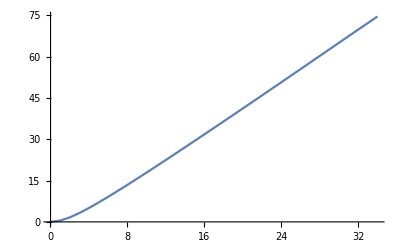

```mathematica
Block[{α=1,mD=1,T=1},DiscretePlot[(√π T α^2 MeijerG[{{1,1,3/2},{}},{{1,2},{0,1/2,1/2}},(mD^2 r^2)/4])/(2 mD^2),{r,0.01,35,1},Filling->None,Joined->True]]
```

```mathematica
Integrate[Ec0[r,α] r^2 ReEs[r,mD,α],r]
```

-(ⅇ^(-mD r) (-4/mD-r) α^2)/mD^2

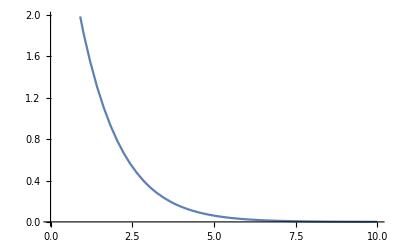

```mathematica
Block[{α=1,mD=1},Plot[-(ⅇ^(-mD r) (-4/mD-r) α^2)/mD^2,{r,0,10}]]
```

```mathematica
Integrate[Ec0[r,α] r^2 ImEs[r,mD,α,T],r]
```

1/16 mD √π r^5 T α^2 MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-5/2,-2}},(mD^2 r^2)/4]

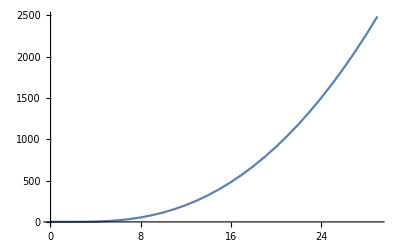

```mathematica
Block[{α=1,mD=1,T=1},DiscretePlot[1/16 mD √π r^5 T α^2 MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-5/2,-2}},(mD^2 r^2)/4],{r,0.01,30,1},Filling->None,Joined->True]]
```

```mathematica
Integrate[Es0[r,α] r^2 ReEc[r,mD,α],r]
```

-(ⅇ^(-mD r) α^2 (2+2 mD r+mD^2 r^2+ⅇ^(mD r) mD^3 r^3 ExpIntegralEi[-mD r]))/(3 mD^3)

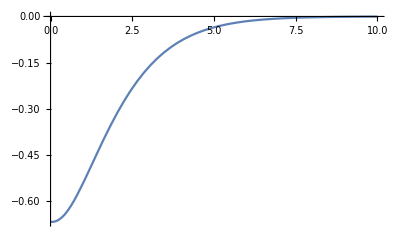

```mathematica
Block[{α=1,mD=1},Plot[-(ⅇ^(-mD r) α^2 (2+2 mD r+mD^2 r^2+ⅇ^(mD r) mD^3 r^3 ExpIntegralEi[-mD r]))/(3 mD^3),{r,0,10}]]
```

```mathematica
Integrate[Es0[r,α] r^2 ImEc[r,mD,α,T],r]
```

-1/8 √π r^4 T α^2 MeijerG[{{-1,0,1/2},{}},{{0,1},{-2,-1/2,-1/2}},(mD^2 r^2)/4]

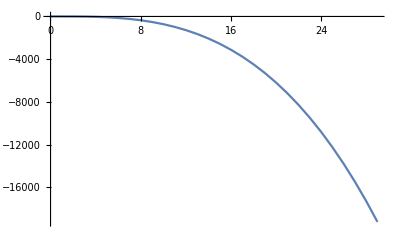

```mathematica
Block[{α=1,mD=1,T=1},DiscretePlot[-1/8 √π r^4 T α^2 MeijerG[{{-1,0,1/2},{}},{{0,1},{-2,-1/2,-1/2}},(mD^2 r^2)/4],{r,0.01,30,1},Filling->None,Joined->True]]
```

```mathematica
Integrate[Es0[r,α] r^2 ReEs[r,mD,α],r]
```

(ⅇ^(-mD r) (-12/mD^3-(12 r)/mD^2-(6 r^2)/mD-r^3) α^2)/mD^2

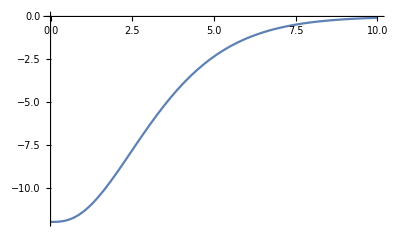

```mathematica
Block[{α=1,mD=1},Plot[(ⅇ^(-mD r) (-12/mD^3-(12 r)/mD^2-(6 r^2)/mD-r^3) α^2)/mD^2,{r,0,10}]]
```

```mathematica
Integrate[Es0[r,α] r^2 ImEs[r,mD,α,T],r]
```

-1/16 mD √π r^7 T α^2 MeijerG[{{-5/2,-1/2,-1/2},{}},{{1/2,1/2},{-7/2,-2,-3/2}},(mD^2 r^2)/4]

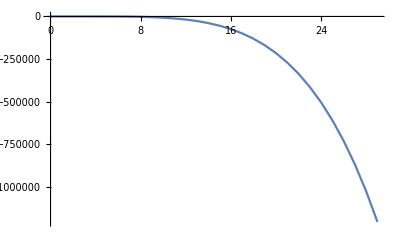

```mathematica
Block[{α=1,mD=1,T=1},DiscretePlot[-1/16 mD √π r^7 T α^2 MeijerG[{{-5/2,-1/2,-1/2},{}},{{1/2,1/2},{-7/2,-2,-3/2}},(mD^2 r^2)/4],{r,0.01,30,1},Filling->None,Joined->True]]
```